# Abstract Muralizer Nonsense

Christoph Maier, 18 May 2009

## Cutting corners when drawing splines à la Cairo

Generate points to feed to the microcontroller, trading off resolution against data rate on a cereal interface.

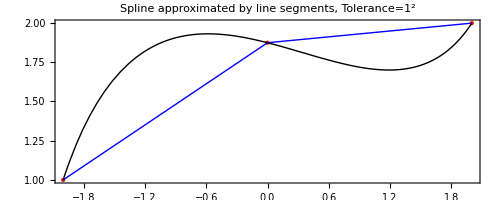

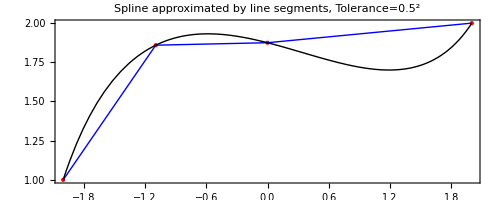

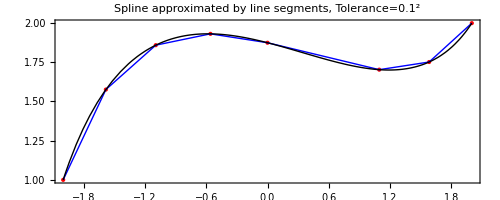

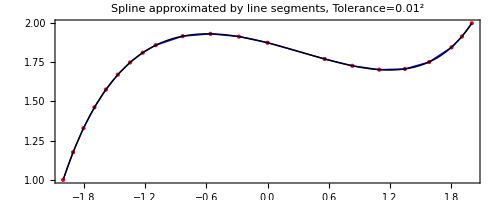

## Bresenham Algorithm Fodder: Spooling out thread to draw a straight line

Or, what's a microcontroller that can't do floating point division supposed to do with the sequence of points?

To draw a straight line from (x_1
y_1) to (x_2
y_2) in Cartesian coordinates, the thread lengths {r,s} of the spools suspended from the points {(X_a
Y_a),(X_b
Y_b)} follow the implicit equation
(r^2 | s^2)·(A | C
C | B)·(r^2
s^2)+D==0
with
(r^2 | s^2)·(OverBar[AB]-ΔAB/2 | C
C | OverBar[AB]+ΔAB/2)·(r^2
s^2)+D==0
and
OverBar[AB]≡(δx^2+δy^2)-2 (δx ΔX+δy ΔY)^2, 
ΔAB≡4 (ΔX δy-δx ΔY) (δy (x-X_0)-δx (y-Y_0)), 
C≡-(δx^2+δy^2),
D≡(ΔX^2+ΔY^2)((ΔX δx+ΔY δy)^2+4 (δy (x-X_0)-δx (y-Y_0))^2),
where
X_0≡(X_a+X_b)/2,
Y_0≡(Y_a+Y_b)/2,
ΔX≡(X_b-X_a)/2,
ΔY≡(Y_b-Y_a)/2,
x≡(x_1+x_2)/2,
y≡(y_1+y_2)/2,
δx≡(x_2-x_1)/2,
δy≡(y_2-y_1)/2.

### How much rope do I give the pen to hang itself?